522.1

16.2

18.4

34.6

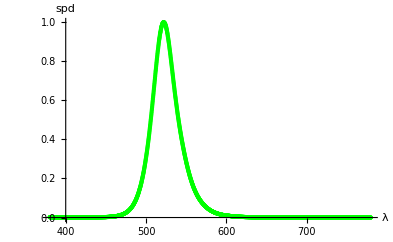

```mathematica
(*通过实验测得的Red LED光谱数据*)
greenSpd=Import["D:\\smartLighting\\smartLighting\\data\\greenSpdData.xls"]//Flatten[#,1]&;
maxGreenSpd=Max[greenSpd[[All,2]]];    (*相对光谱峰值大小，应该为1*)
greenSpd[[All,2]]=greenSpd[[All,2]]/maxGreenSpd; (*归一化*)

Nearest[greenSpd[[All,2]],1,4];   (*取出最大的4个峰值，观察特点*)
greenCenterLamda=Nearest[greenSpd[[All,2]]->greenSpd[[All,1]],1,4];       
greenCenterLamda= (greenCenterLamda[[1]]+greenCenterLamda[[2]])/2(*峰值处对应的波长,这次要求平均数*)

greenHwList=Nearest[greenSpd[[All,2]],0.5,4];     (*spd数值为峰值波长的一半的左右N点峰值大小*)
greenHwList=Nearest[greenSpd[[All,2]]->greenSpd[[All,1]],0.5,4] ;    (*spd数值为峰值波长的一半的左右4点波长坐标*)

greenHwL=greenCenterLamda-(greenHwList[[3]]+greenHwList[[4]])/2 //Abs          (*波长半宽左边*)
greenHwR=(greenHwList[[1]]+greenHwList[[2]])/2-greenCenterLamda //Abs         (*波长半宽右边*)
greenHW=(greenHwList[[3]]+greenHwList[[4]]-greenHwList[[1]]-greenHwList[[2]] )/2//Abs          (*半波宽*)

gGreenLed=ListPlot[greenSpd,PlotRange->{{380,780},{0,1}},(*AxesOrigin->{370*10^-9,0},*)AxesLabel->{"λ","spd"},PlotStyle->{Green},PlotLegends->"Expressions"]
```

```mathematica
(*(*λp=607.8*10^-9;
hw=18.6*10^-9;*)

(*(*高斯模型*)
spd[λ_]=Exp[-4 Log[2]*(λ-λp)^2/hw^2];
maxSpd=Maximize[spd[λ],λ];
rSpd[λ_]:=spd[λ]/maxSpd[[1]];
(*rSpd[λ_]:=cofSpd*spd[λ];*)

g2=Plot[rSpd[x],{x,380*10^-9,780*10^-9},PlotRange->{0,1},PlotLegends->"Expressions"];
*)
(*(*Yoshi，2004模型*)
g[λ_]:=Exp[-(λ-λp)^2/hw^2];
yoshiSpd[λ_]:=(g[λ]+2g[λ]^5)/3;
maxYoshiSpd=Maximize[spd[λ],λ];
rYoshiSpd[λ_]:=yoshiSpd[λ]/maxYoshiSpd[[1]];
g3=Plot[rYoshiSpd[x],{x,380*10^-9,780*10^-9},PlotRange->{0,1},PlotStyle->{Green},PlotLegends->"Expressions"];

*)
(*(*潘建根，2005模型,存在求出的最大值与画图得到的最大值不相符的问题 ；；； OK,用NMaximize解决*)
panSpd[λ_]:=Exp[-3.2213(λ-λp)^2/hw^2]*Exp[-0.3*Abs[(λ-λp)/hw]];

maxPanSpd=NMaximize[{panSpd[λ],500*10^-9<=λ≤700*10^-9},λ];

rPanSpd[λ_]:=panSpd[λ]/maxPanSpd[[1]];
g4=Plot[rPanSpd[x],{x,380*10^-9,780*10^-9},PlotRange->{0,1},PlotStyle->{ Pink},PlotLegends->"Expressions"];

*)
(**************测试图形***************)
(*Manipulate[Show[Plot[Cosh[k2*x^2],{x,-2Pi,2Pi},PlotRange->{-20,20}],Plot[Cosh[k2*x^2]^0.5,{x,-2Pi,2Pi},PlotRange->{-20,20},PlotStyle->{ Green,Thickness[0.004]}],Plot[Cosh[k2*x^2]^0.4,{x,-2Pi,2Pi},PlotRange->{-20,20},PlotStyle->{ Red,Thickness[0.004]}]],{{k2,4.83,"k2"},-100,100,0.1,Appearance->"Labeled"}];*)





(*2006 年 Kwong Man 和 Ian Ashdown 等人提出的双高斯模型*)


(*杨武，2012模型*)
(*ywSpd[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{Exp[-k1L*(x-greenCenterLamda)^2/(greenHwL*2)^2]*Cosh[k2L*(x-greenCenterLamda)^2/(greenHwL*2)^2],380*10^-9≤x<=greenCenterLamda[[1]]},{Exp[-k1R*(x-greenCenterLamda)^2/(greenHwR*2)^2]*Cosh[k2R*(x-greenCenterLamda)^2/(greenHwR*2)^2],greenCenterLamda[[1]]<x<=780*10^-9}}];
  
g5=Plot[ywSpd[x,k1L,k2L,k1R,k2R],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,1}},PlotStyle->{ Green,Thickness[0.004]},PlotLegends->"Expressions"];

Manipulate[Show[g1,Plot[ywSpd[x,k1L,k2L,k1R,k2R],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,1}},PlotStyle->{ Green,Thickness[0.004]},PlotLegends->"Expressions"]],{{k1L,k1L,"k1L"},0,10,0.0001,Appearance->"Labeled"},{{k2L,k2L,"k2L"},-10,10,0.0001,Appearance->"Labeled"},{{k1R,k1R,"k1R"},0,10,0.0001,Appearance->"Labeled"},{{k2R,k2R,"k2R"},-10,10,0.0001,Appearance->"Labeled"}];*)


(*Show[g1,g2,g3,g4,g51,g52]*)



(*====================================分割线=======================================*)

(*g[x_]:=Exp[-(x-λp)^2/hw^2];
yoshiSpd[x_]:=(g[x]+2g[x]^5)/3;*)

testSpd[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{((Exp[-k1L*(x-greenCenterLamda)^2/(greenHwL*3)^2]+2*Exp[-k1L*(x-greenCenterLamda)^2/(greenHwL*3)^2]^5)/3)*Cosh[k2L*(x-greenCenterLamda)^2/(greenHwL*3)^2]^-0.1,380*10^-9≤x<=greenCenterLamda},{((Exp[-k1R*(x-greenCenterLamda)^2/(greenHwR*2)^2]+2*Exp[-k1R*(x-greenCenterLamda)^2/(greenHwR*2)^2]^5)/3)*Cosh[k2R*(x-greenCenterLamda)^2/(greenHwR*2)^2]^0.1,greenCenterLamda<x<=780*10^-9}}];
g6=Plot[testSpd[x,k1L,k2L,k1R,k2R],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,1}},PlotStyle->{ Green,Thickness[0.004]},PlotLegends->"Expressions"];

Manipulate[Show[g1,Plot[testSpd[x,k1L,k2L,k1R,k2R],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,1}},PlotStyle->{ Green,Thickness[0.004]},PlotLegends->"Expressions"]],{{k1L,2.328,"k1L"},0,5,0.0001,Appearance->"Labeled"},{{k2L,13.249,"k2L"},-2,20,0.001,Appearance->"Labeled"},{{k1R,0.6667,"k1R"},-2,10,0.0001,Appearance->"Labeled"},{{k2R,-0.3175,"k2R"},-20,10,0.0001,Appearance->"Labeled"}]*)
```